# Mathematica for Research

### Student Information Name : Harshad Kumar Elangovan Student ID : 19200349 Course : Data and Computational Science Assignment Number : 07 Due date : "Thu 7 Nov 2019 14:00:00""GMT"

### Analytically solving equations

Find the fifth roots of 7 (five of them) by writing out a suitable equation to solve and then using Solve. Print out approximate numerical values. Check that you’ve found the right values by substituting back into the equation you solved.

```mathematica
equation1 = x^5-7==0;
```

```mathematica
val1=Solve[equation1,x]
```

{{x→-(-7)^(1/5)},{x→7^(1/5)},{x→(-1)^(2/5) 7^(1/5)},{x→-(-1)^(3/5) 7^(1/5)},{x→(-1)^(4/5) 7^(1/5)}}

```mathematica
val1//N
```

{{x→-1.19393-0.867438 ⅈ},{x→1.47577},{x→0.456039+1.40354 ⅈ},{x→0.456039-1.40354 ⅈ},{x→-1.19393+0.867438 ⅈ}}

Verification:

```mathematica
equation1/.val1
```

{True,True,True,True,True}

OR

```mathematica
x^5-7/.val1
```

{0,0,0,0,0}

Using the Reduce function, or otherwise, find the range of values of x for which x^4+6 x^3-21 x^2-74x+168>0.

```mathematica
Reduce[x^4+6 x^3-21 x^2-74 x + 168 >0,{x}]
```

x<-7||-4<x<2||x>3

Use Solve to find the solutions to P_3^(1,1)(x)=p for x as a function of p, where P_l^(a,b)(x) is a Jacobi polynomial (available as JacobiP[l, a, b, x] in Mathematica)

```mathematica
JacobiP[3,1,1,x]
```

4+18 (-1+x)+21 (-1+x)^2+7 (-1+x)^3

```mathematica
Solve[Subscript[P, 3]^(1,1)(x)== p,x]
```

{{x→(2/7)^(1/3)/((7 p+√7 √(-4+7 p^2))^(1/3))+((7 p+√7 √(-4+7 p^2))^(1/3))/(2^(1/3) 7^(2/3))},{x→-(1+ⅈ √3)/(2^(2/3) 7^(1/3) (7 p+√7 √(-4+7 p^2))^(1/3))-((1-ⅈ √3) (7 p+√7 √(-4+7 p^2))^(1/3))/(2 2^(1/3) 7^(2/3))},{x→-(1-ⅈ √3)/(2^(2/3) 7^(1/3) (7 p+√7 √(-4+7 p^2))^(1/3))-((1+ⅈ √3) (7 p+√7 √(-4+7 p^2))^(1/3))/(2 2^(1/3) 7^(2/3))}}

Jacobi polynomial can also be defined as:

```mathematica
Solve[JacobiP[3,1,1,x]==p,x]
```

{{x→(2/7)^(1/3)/((7 p+√7 √(-4+7 p^2))^(1/3))+((7 p+√7 √(-4+7 p^2))^(1/3))/(2^(1/3) 7^(2/3))},{x→-(1+ⅈ √3)/(2^(2/3) 7^(1/3) (7 p+√7 √(-4+7 p^2))^(1/3))-((1-ⅈ √3) (7 p+√7 √(-4+7 p^2))^(1/3))/(2 2^(1/3) 7^(2/3))},{x→-(1-ⅈ √3)/(2^(2/3) 7^(1/3) (7 p+√7 √(-4+7 p^2))^(1/3))-((1+ⅈ √3) (7 p+√7 √(-4+7 p^2))^(1/3))/(2 2^(1/3) 7^(2/3))}}

### Numerically solving equations

Use NSolve to numerically find all 7 roots of the polynomial
 -3686400+92039680 x-396518848 x^2+628548544 x^3- 465151532 x^4+166874096 x^5-25586945 x^6+916500 x^7

```mathematica
equation2=-3686400+92039680 x-396518848 x^2+628548544 x^3- 465151532 x^4+166874096 x^5-25586945 x^6+916500 x^7;
```

```mathematica
NSolve[equation2==0,x]
```

{{x→0.05},{x→0.382979},{x→1.28},{x→1.53846},{x→2.},{x→2.66667},{x→20.}}

In general there may not be an analytic solution to a nonlinear equation and the FindRoot method can be useful. Consider the implicit equation u/7=(2-w^2-2 cos w)/(2 w). In this case Reduce and Solve can’t find a solution for w as a function of u. Create a function which takes one argument (u) and uses FindRoot to numerically solve for w for the given numeric value of u. (Hint: use w=1 as a starting guess in FindRoot)

```mathematica
f[u_]:= FindRoot[u/7== (2-w^2-2 Cos[w])/(2 w),{w,1}]
```

```mathematica
f[1]
```

{w→-1.54848}

Plot the function from the previous question for -2π≤u≤4π

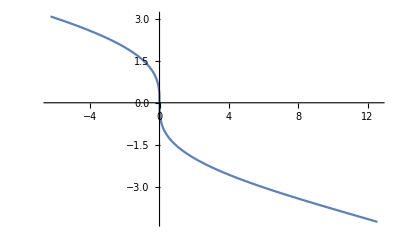

```mathematica
Plot[Values[f[u]],{u,-2 π,4 π}]
```

### Analytically solving partial differential equations

The Black-Scholes equation is used to model financial markets. It is a partial differential equation for the function V(t,S) representing the value of an option as a function of the price of the underlying asset, S, and time, t. The differential equation features two parameters: σ, the standard deviation of the stock’s returns; and r, the annualized risk-free interest rate. The Black-Scholes equation is given by

(∂V)/(∂t)+1/2 σ^2 S^2(∂^2 V)/(∂S^2)+r S (∂V)/(∂S)-r V=0
With a strike price K, the Black-Scholes equation may be solved with boundary condition at the expiry time, T, of V(T,S)=max(S-K,0).

Use DSolve to solve the Black-Scholes equation as described above.

```mathematica
equation5= {D[V[t,S],t]+(σ^2 S^2 D[V[t,S],{S,2}])/2+r S D[V[t,S],S]-r V[t,S]==0,V[T,S]==Max[S-K,0]};
```

```mathematica
val1= V[t,S]/.DSolve[equation5,V[t,S],{t,S}]
```

{1/2 ⅇ^(-r T) (-ⅇ^(r t) K Erfc[((t-T) (2 r-σ^2)+2 Log[K]-2 Log[S])/(2 √2 √(-t+T) σ)]+ⅇ^(r T) S Erfc[((t-T) (2 r+σ^2)+2 Log[K]-2 Log[S])/(2 √2 √(-t+T) σ)])}

Use the solution to compute the value of an option with T=1, S=14, K=15, σ=0.3, r=0.03 at time t=0

```mathematica
val1/. {T->1,S->14,K->15,σ->0.3,r->0.03,t->0}
```

{1.43839}

### Numerically solving ordinary differential equations

The equations for the trajectory of an orbit around a black hole are given by
(d^2 r)/dt^2-(L^2(r-3M))/r^4+M/r^2=0
dϕ/dt-L/r^2=0
where r(t) and ϕ(t) are polar coordinates and M and L are constants.

Use NDSolve to solve these equations in the case M=1, L=72/(√395) with initial conditions r(0)=36/5, r'(0)=-√(5/474),ϕ(0)=0 over the time range t∈[0,1000].

```mathematica
ClearAll[r,t,L,M,t,val1]
L=72/Sqrt[395];
M=1;
val=NDSolve[{r''[t]-((L^2 (r[t]-3 M))/r[t]^4)+M/r[t]^2==0,ϕ'[t]-L/r[t]^2==0,r[0]==36/5,r'[0]==-Sqrt[(5/474)],ϕ[0]==0},{r,ϕ},{t,0,1000}]
```

{{r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

Using the standard relationship between polar and Cartesian coordinates (x=r cos ϕ,y=r sin ϕ) create a plot of the orbit as represented by the parametric curve (x(t), y(t))

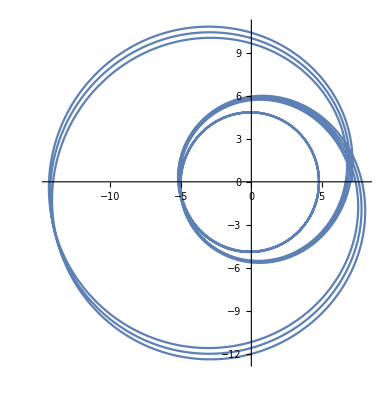

```mathematica
ParametricPlot[{r[t] Cos[ϕ[t]],r[t] Sin[ϕ[t]]}/.val,{t,0,1000}]
```